## 1. Логический оператор AND как пример линейно разделимых классов

```mathematica
Train = {{-1,-1,-1},{-1,1,-1},{1,-1,-1},{1,1,1}};
```

```mathematica
X=Train⟦All,1;;2⟧;
Y = Train⟦;;,3⟧;
```

```mathematica
iCold = {1,2,3};
iWarm = {4};
```

```mathematica
Fig0=Graphics[
MapThread[{#2/.{-1->Blue,1->Red},PointSize[Large],Point[#1]}&,{X,Y}],
Frame->True,GridLines->Automatic
];
```

```mathematica
W = RandomReal[{-2,2},3]
```

{-0.798013,0.12619,-0.336978}

```mathematica
SVM[W_List, x_List]:=W.Prepend[x,-1]
```

```mathematica
Show[Fig0,ContourPlot[SVM[W,{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}]];
```

## 2. Задача условной оптимизации

```mathematica
wtext=Table[Symbol["W"<>ToString[i]],{i,0,2}]
```

{W0,W1,W2}

```mathematica
condition=MapThread[#2*(wtext.Prepend[#1,-1])≥1&,{X,Y}]
```

{W0+W1+W2≥1,W0+W1-W2≥1,W0-W1+W2≥1,-W0+W1+W2≥1}

```mathematica
W=FindMinimum[{Rest[wtext].Rest[wtext],And@@condition},wtext]//Last//Values
```

{1.,1.,1.}

```mathematica
Show[Fig0,ContourPlot[SVM[W,{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}]];
```

## 3. Логический оператор XOR и повышение размерности фазового пространства

```mathematica
Train = {{-1,-1,-1},{-1,1,1},{1,-1,1},{1,1,-1}};
```

```mathematica
X=Train⟦All,1;;2⟧;
Y = Train⟦;;,3⟧;
```

```mathematica
iCold = {1,4};
iWarm = {2,3};
```

```mathematica
Fig0=Graphics[
MapThread[{#2/.{-1->Blue,1->Red},PointSize[Large],Point[#1]}&,{X,Y}],
Frame->True,GridLines->Automatic
];
```

```mathematica
XX={First[#],Last[#],(First[#]+Last[#])^2/4}&/@X
```

{{-1,-1,1},{-1,1,0},{1,-1,0},{1,1,1}}

```mathematica
W = RandomReal[{-2,2},4]
```

{-0.213149,1.0955,0.484938,-1.18751}

```mathematica
Show[Fig0,ContourPlot[SVM[W,{x,y,(x+y)^2/4}],{x,-1.5,1.5},{y,-1.5,1.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}]];
```

```mathematica
wtext=Table[Symbol["W"<>ToString[i]],{i,0,3}]
```

{W0,W1,W2,W3}

```mathematica
condition=MapThread[#2*(wtext.Prepend[#1,-1])≥1&,{XX,Y}]
```

{W0+W1+W2-W3≥1,-W0-W1+W2≥1,-W0+W1-W2≥1,W0-W1-W2-W3≥1}

```mathematica
W=FindMinimum[{Rest[wtext].Rest[wtext],And@@condition},wtext]//Last//Values//Chop
```

{-1.,0,0,-2.}

```mathematica
Show[Fig0,ContourPlot[SVM[W,{x,y,(x+y)^2/4}],{x,-1.5,1.5},{y,-1.5,1.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}]];
```

```mathematica
Show[Graphics3D[MapThread[{#2/.{-1->Blue,1->Red},PointSize[Large],Point[#1]}&,{XX,Y}]],
ContourPlot3D[SVM[W,{x,y,z}],{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.5,1.5},
Contours->{-1,0,1},ContourStyle->{{Opacity[0.6],Blue},{Opacity[0.2],Yellow},{Opacity[0.6],Red}},Mesh->None]];
```

## 4. Метод опорных векторов

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Dimensions[Train=Import["NG22P05Problem.xlsx",{"Sheets","ГолубовичР"}][[2;;]]]
```

{4905,3}

```mathematica
Dimensions[Train=DeleteCases[Train,Last[Train]]]
```

{4792,3}

```mathematica
X=Train⟦All,1;;2⟧;
Y = Train⟦;;,3⟧//Round;
```

```mathematica
iCold=Flatten[Position[Y,-1]];
iWarm=Flatten[Position[Y,1]];
```

```mathematica
Fig0=Graphics[
MapThread[{#2/.{-1->Blue,1->Red},Point[#1]}&,{X,Y}],
Frame->True,GridLines->Automatic
];
```

```mathematica
iksi[{x1_,x2_}]:=Flatten@Table[Table[x1^(i-k)*x2^k,{k,0,i}],{i,1,4}]
```

```mathematica
iksi[{x,y}]
```

{x,y,x^2,x y,y^2,x^3,x^2 y,x y^2,y^3,x^4,x^3 y,x^2 y^2,x y^3,y^4}

```mathematica
XX=iksi[#]&/@X;
```

```mathematica
Dynamic@W
```

```mathematica
resW={1.13433,7.73537,-8.36949,-7.23486,-4.90809,7.29278,-2.96806,-6.04722,-0.116828,0.68038,3.65224,-7.0287,1.41803,-6.891,-1.76189}
```

{1.13433,7.73537,-8.36949,-7.23486,-4.90809,7.29278,-2.96806,-6.04722,-0.116828,0.68038,3.65224,-7.0287,1.41803,-6.891,-1.76189}

```mathematica
W = resW
```

{1.13433,7.73537,-8.36949,-7.23486,-4.90809,7.29278,-2.96806,-6.04722,-0.116828,0.68038,3.65224,-7.0287,1.41803,-6.891,-1.76189}

```mathematica
Margin=MapThread[#2(W0.Prepend[#1,-1])&,{XX,Y}];
```

```mathematica
Position[Margin,1.]
```

{}

```mathematica
iS=Position[Round[Margin,0.0001],1.]//Flatten
```

{}

```mathematica
SVM[W,iksi[{1,1}]]
```

-25.6817

```mathematica
Show[
Fig0,
ContourPlot[
SVM[W,iksi[{x,y}]],{x,-2,2},{y,-2,2},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}
],
{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧//Graphics
];
```

## 5. Опорные точки

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P05 GolubovichRoman

```mathematica
Dimensions[Train=Rest[Import["NG22P05Problem.xlsx",{"Sheets","Train"}]]]
```

{180,3}

```mathematica
X=Train⟦All,1;;2⟧;
Y = Round[Train⟦;;,3⟧];
```

```mathematica
iCold=Flatten[Position[Y,-1]];
iWarm=Flatten[Position[Y,1]];
```

```mathematica
Fig0=Graphics[
MapThread[{#2/.{-1->Blue,1->Red},Point[#1]}&,{X,Y}],
Frame->True,GridLines->Automatic
];
```

```mathematica
iksi2[{x1_,x2_}]:=Flatten@Table[Table[x1^(i-k)*x2^k,{k,0,i}],{i,1,2}]
```

```mathematica
iksi2[{x,y}]
```

{x,y,x^2,x y,y^2}

```mathematica
XX=iksi[#]&/@X;
```

```mathematica
W = RandomReal[{-2,2},6]
```

{0.695127,-1.83687,-0.423352,-0.615739,1.05826,0.735733}

```mathematica
{iS,iC}=Partition[RandomSample[Range[Length[X]],8],4]
```

{{139,44,100,134},{8,33,82,67}}

```mathematica
Show[Fig0,ContourPlot[SVM[W,iksi2[{x,y}]],{x,-2.5,2.5},{y,-2.5,2.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}],
Graphics[{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧],
Graphics[{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧]
];
```

```mathematica
CreatePalette[Dynamic@Show[Fig0,ContourPlot[SVM[W,iksi2[{x,y}]],{x,-2.5,2.5},{y,-2.5,2.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}],
Graphics[{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧],
Graphics[{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧]]]
```

vf4ri_shm19FrontEndObject[LinkObject["vf4ri_shm", 3, 1]]19Untitled-2

## 6. Множители Лагранжа и формулировка двойственной задачи

```mathematica
lambdas=Table[Symbol["λ"<>ToString[i]],{i,Length[iS]}]
```

{λ1,λ2,λ3,λ4}

```mathematica
With[
{len=Length[iS],Ys=Y⟦iS⟧,Xs=XX⟦iS⟧},
Expand[-Total[lambdas]+1/2∑_(i=1)^len ∑_(j=1)^len lambdas⟦i⟧lambdas⟦j⟧Ys⟦i⟧Ys⟦j⟧(Xs⟦i⟧.Xs⟦j⟧)
]]
```

-λ1+15.304 λ1^2-λ2+3.71286 λ1 λ2+14.9411 λ2^2-λ3-2.51479 λ1 λ3+0.0269184 λ2 λ3+0.173979 λ3^2-λ4+16.7012 λ1 λ4+3.4666 λ2 λ4-1.39897 λ3 λ4+7.03721 λ4^2

```mathematica
Apply[And,((#≥0)&/@lambdas)]
```

λ1≥0&&λ2≥0&&λ3≥0&&λ4≥0

```mathematica
lambdas.Y⟦iS⟧==0
```

-λ1-λ2+λ3-λ4==0

```mathematica
Qss=With[{YXX=Y⟦iS⟧XX⟦iS⟧},Outer[Dot,YXX,YXX,1]]
```

{{30.6079,3.71286,-2.51479,16.7012},{3.71286,29.8823,0.0269184,3.4666},{-2.51479,0.0269184,0.347957,-1.39897},{16.7012,3.4666,-1.39897,14.0744}}

```mathematica
Expand[1/2 Qss.#.#-Total[#]]&@lambdas
```

-λ1+15.304 λ1^2-λ2+3.71286 λ1 λ2+14.9411 λ2^2-λ3-2.51479 λ1 λ3+0.0269184 λ2 λ3+0.173979 λ3^2-λ4+16.7012 λ1 λ4+3.4666 λ2 λ4-1.39897 λ3 λ4+7.03721 λ4^2

```mathematica
Y⟦iS⟧.lambdas==0
```

-λ1-λ2+λ3-λ4==0

## 7. Последовательный метод активных ограничений

### 7.1. Инициализация множества опорных точек.

```mathematica
iSW=First[RandomChoice[iWarm,1]];
iSC=First[Nearest[X⟦iCold⟧->iCold,X⟦iSW⟧]];
iSWN=First[Nearest[X⟦iWarm⟧->iWarm,X⟦iSC⟧]]
```

168

```mathematica
iS=Module[{iSC=First[RandomChoice[iCold,1]],iSW},
FixedPoint[(iSW=First[Nearest[X⟦iWarm⟧->iWarm,X⟦#⟧]]; First[Nearest[X⟦iCold⟧->iCold,X⟦iSW⟧]])&,iSC];
{iSC,iSW}
]
```

{15,150}

```mathematica
Y⟦iS⟧
```

{-1,1}

### 7.2. Построение разделительной полосы

```mathematica
iC={};
iO=Complement[Range[Length[X]],iS,iC];
```

```mathematica
lambdas=Table[Symbol["λ"<>ToString[i]],{i,Length[iS]}];
```

```mathematica
Qss=With[{YXX=Y⟦iS⟧XX⟦iS⟧},Outer[Dot,YXX,YXX,1]];
```

```mathematica
lambdasNumbers=Values[(FindMinimum[{Expand[1/2 Qss.#.#-Total[#]],Y⟦iS⟧.#==0},#]&@lambdas)[[2]]];
```

```mathematica
W=Total[lambdasNumbers*Y⟦iS⟧*XX⟦iS⟧];
```

```mathematica
iL=Flatten[Position[lambdasNumbers,_?Positive]];
```

```mathematica
W0=Median[W.XX⟦#⟧-Y⟦#⟧&/@iS⟦iL⟧];
```

```mathematica
CreatePalette@Dynamic@Show[Fig0,ContourPlot[SVM[Prepend[W,W0],iksi[{x,y}]],{x,-2.5,2.5},{y,-2.5,2.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}],
Graphics[{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧],
Graphics[{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧]]
```

r2rej_shm19FrontEndObject[LinkObject["r2rej_shm", 3, 1]]19Untitled-2

### 7.3 Провера опорных точек

```mathematica
If[
Length[iS]>2,
iLC=Flatten[Position[lambdasNumbers,_?NonPositive]];
If[
Length[iLC]>0, 
iCN=First[TakeSmallest[lambdasNumbers->"Index",1]];
AppendTo[iC,iS⟦iCN⟧];
iS=Drop[iS,{iCN}]
]
];
```

### 7.4 Ложная опорная точка

```mathematica
If[
Length[iC]>0,
AppendTo[iO,First[iC]];
iC={};
];
```

### 7.5 Отступы

```mathematica
Mo=Y⟦#⟧(W.XX⟦#⟧-W0)&/@iO;
```

```mathematica
{Mn,iMn}=First[TakeSmallest[Mo->{"Element","Index"},1]];
```

```mathematica
With[{MniMn=First[TakeSmallest[Mo->{"Element","Index"},1]]},
If[MniMn[[1]]<1,
AppendTo[iC,iO⟦MniMn[[2]]⟧];iO=Drop[iO,{MniMn[[2]]}];
]];
```

### 7.6 Новая опорная точка

```mathematica
If[
Length[iC]>0,
AppendTo[iS,First[iC]];
iC={};
];
```

### 7.7 Конец алгоритма

```mathematica
Length[#]&/@{iS,iC,iO}
```

{9,0,171}

```mathematica
resW2={0.0148418,-0.341416,-0.176574,-0.0742703,-0.199513,0.0169681,0.0622791,0.121766,-0.213784,-0.373391,-0.170741,-0.254662,-0.14582,-0.698222}
```

{0.0148418,-0.341416,-0.176574,-0.0742703,-0.199513,0.0169681,0.0622791,0.121766,-0.213784,-0.373391,-0.170741,-0.254662,-0.14582,-0.698222}

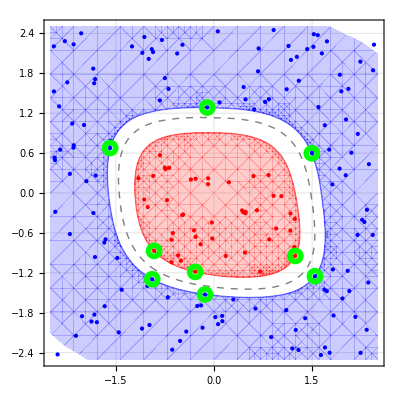

```mathematica
Show[
Fig0,
ContourPlot[
SVM[Prepend[W,W0],iksi[{x,y}]],{x,-2.5,2.5},{y,-2.5,2.5},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}
],
Graphics[{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧],
Graphics[{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧]
]
```